```mathematica
g[R_]:=1/(10004000600040001 R^2)(-7998400080000 R+9000299950001 R^2-1000200010000 R^3+600 √1111 √(-99870049995000129999 R^2+299750038003799750003 R^3-299889986001400109997 R^4+100009997999800010001 R^5))
```

```mathematica
h[R_]:=g[R+1]
```

```mathematica
g1[R_]:=1/(1004006004001 R^2)(-7984008000 R+9002995001 R^2-1002001000 R^3+60 √1110 √(-987049950012999 R^2+2975038037975003 R^3-2988986014010997 R^4+1000997998001001 R^5))
```

```mathematica
h1[R_]:=g1[R+1]
```

```mathematica
g2[R_]:=(-7840800 R+9029501 R^2-1020100 R^3+60 √11 √(-8749501299 R^2+27538377503 R^3-28886141097 R^4+10097980101 R^5))/(104060401 R^2)
```

```mathematica
h2[R_]:=g2[R+1]
```

```mathematica
g3[R_]:=(-6480 R+9251 R^2-1210 R^3+6 √10 √(-15129 R^2+91553 R^3-177507 R^4+107811 R^5))/(14641 R^2)
```

```mathematica
h3[R_]:=g3[R+1]
```

```mathematica
g4[R_]:=(-16 R+75 R^2-18 R^3+2 √2 √(-49 R^2+105 R^3+117 R^4+27 R^5))/(81 R^2)
```

```mathematica
h4[R_]:=g4[R+1]
```

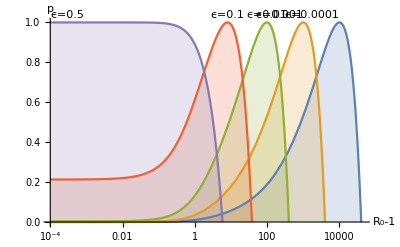

```mathematica
LogLinearPlot[{h[R],h1[R],h2[R],h3[R],h4[R]},{R,0.0001,48000},AxesLabel->{"R_0-1",p},PlotRange->{{0.0001,45000},{0,1}},Filling->Bottom,PlotLabels->Placed[{"ϵ=0.0001","ϵ=0.001","ϵ=0.01","ϵ=0.1","ϵ=0.5"},Above]]
```

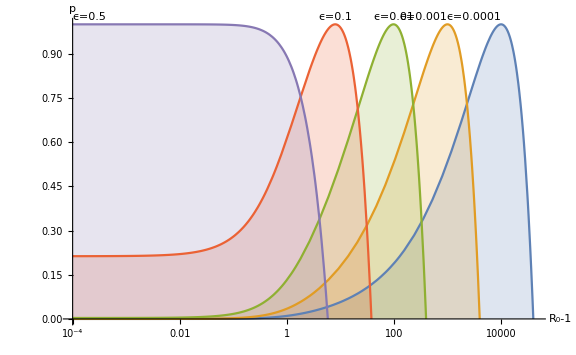

```mathematica
Show[%27,ImageSize->Large]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Documents\\GitHub\\RogerZhang\\Project_Draft\\Supplementary_material\\Figures\\Epsilons.pdf",%28,"PDF"]
```

C:\Users\Roger Zhang\Documents\GitHub\RogerZhang\Project_Draft\Supplementary_material\Figures\Epsilons.pdf